## Crop hearts from 3D+Time MRI images

Images in the dataset we used (MnMs) are taken with  Breath-Hold technique. This means that the only movement in the image will be the heart pumping motion.
This code can find the rough position of the heart in a MRI image by finding the center of motion and by fitting a 2D gaussian curve to it. By slicing the gaussian ad a chosen confidence interval we can crop the heart from the image.

```mathematica
selectUseful = image ↦ (
	data = ImageData[image //Binarize];
	height = Length[data];
	width = Length[data[[1]]];
	breadth = Length[data[[1, 1]]];
	count = Total@Flatten@data / (width*height*breadth);
	Or[count < .05, count > .95]
); (*TODO ADJUST PARAMETERS FOR 3D*)

getAverage = layer ↦ (
	frameCount = layer //Length;
	differences = GaussianFilter /@ MeanFilter[#, 4] &/@ImageAdjust /@ (layer[[2;;frameCount]] - layer[[1;;frameCount-1]] ); (*NonlocalMeansFilter?*)
	usefulDifferences = Select[differences, selectUseful];
	dataset = (If[ImageMeasurements[#1, "Mean"] <.5, #1, 1-#1] &/@ Binarize /@ usefulDifferences) ~ Select ~ (Max[MorphologicalComponents[#]] <= 100&);
	If[Length[dataset] == 0, Throw["no images"]];
	{
		Mean[layer] // ImageAdjust,
		Binarize[Mean[dataset], Method->{"BlackFraction", 0.95}]  ~DeleteSmallComponents~10000
	}
);
```

```mathematica
FitGauss3D = image ↦ (
	data=ImageData[image, DataReversed->True];
	min=Min[data];
	sum=Total[data-min,Infinity];
	p=(data-min)/sum;
	{l, m,n}=Dimensions[p];
	mean=N@Sum[{i,j, k} p[[i,j, k]],{i,1,l},{j,1,m}, {k, 1, n}];
	cov=Sum[Outer[Times,{i,j,k}-mean,{i,j,k}-mean] p[[i,j,k]],{i,1,l},{j,1,m},{k,1,n}];
	rot = {{0, 0, 1}, {0, -1, 0}, {1, 0, 0}};

	{
		mean[[-1;;1;;-1]],
		Inverse[rot].cov.rot
	}
);

GetHeartBB[image_, sigma_ : 8] := (
	{ cm, cov } = FitGauss3D[image] //N;
	ell = Ellipsoid[cm, cov*sigma];
	BoundingRegion[ell]
)
```

```mathematica
HighlightHeart[background_, image_, sigma_ :8] := (
Show[Graphics3D@{
		Opacity[.5],
		GetHeartBB[image, sigma]
	}, background, BoxRatios->{1, 1, 1}]
);

CropHeart = {image3D, bbCuboid} ↦ (
	imgData = ImageData[image3D, DataReversed->True];
	
	boundaries = Map[Round, {bbCuboid[[1]], bbCuboid[[2]]} // Transpose, 2] (*x, y, z*);
	
	{{a, b}, {c, d}, {e, f}} = {boundaries[[3]], boundaries[[1]], boundaries[[2]]};
	
	imgData[[
		Max[a, 1] ;; Min[b, (Dimensions@imgData)[[1]]],
		Max[e, 1] ;; Min[f, (Dimensions@imgData)[[2]]],
		Max[c, 1] ;; Min[d, (Dimensions@imgData)[[3]]]
	]] // Image3D // ImageAdjust (*ImageAdjust is needed to renormalize image histogram after cropping. No data is lost!*)
);

heartRegions = <||>;
CropFile[filename_, outputfileED_, outputfileES_, ED_, ES_] := (
	file = Import[filename];
	sigma = 8;
	
	result = "";
	result = Catch[
		avg = getAverage[Image3D /@ file[[1]]];
		heartRegion = GetHeartBB[avg[[2]], sigma];
		
		croppedHeartED = CropHeart[file[[1, ED+1, ;;]] // Image3D, heartRegion];
		croppedHeartES = CropHeart[file[[1, ES+1, ;;]] // Image3D, heartRegion];
	];
	
	Export[outputfileED, If[result == Null, croppedHeartED, "{}", "{}"]];
	Export[outputfileES, If[result == Null, croppedHeartES, "{}", "{}"]];
	(*PrintTemporary[filename];*)
	filename -> heartRegion
)

CropLabel[labelname_, heartRegion_, outputfileED_, outputfileES_, ED_, ES_] := ( (*TODO*)
	label = Import[labelname];
	result = "";
	result = Catch[
		croppedLabelED = CropHeart[label[[1, ED+1, ;;]] // Image3D, heartRegion];
		croppedLabelES = CropHeart[label[[1, ES+1, ;;]] // Image3D, heartRegion];
	];
	Export[outputfileED, If[result == Null, croppedLabelED, "{}", "{}"]];
	Export[outputfileES, If[result == Null, croppedLabelES, "{}", "{}"]];
	(*PrintTemporary[labelname];*)
)
```

## Example usage

```mathematica
(*Approx 98% confidence interval: InverseCDF[ChiSquareDistribution[2],0.98] == 7.82*)
nifti = Import["/Users/matteo/Desktop/sani/Sani Siemens/A2N8V0/A2N8V0_sa.nii.gz"];
img3d = Image3D /@nifti[[1]];
```

```mathematica
average = getAverage@img3d
```

{-Graphics3D-,-Graphics3D-}

```mathematica
{cm, cov} = FitGauss3D[average[[2]]]
```

{{80.8011,108.395,4.92326},{{291.876,-74.034,9.48413},{-74.034,224.281,6.24812},{9.48413,6.24812,8.52423}}}

```mathematica
HighlightHeart[average[[1]], average[[2]]]
```

-Graphics3D-

-Graphics3D-

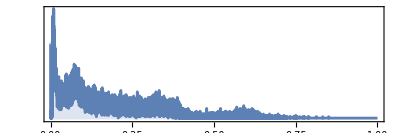

```mathematica
cropped = CropHeart[average[[1]], GetHeartBB[average[[2]]]]
ImageHistogram[cropped, All]
```

```mathematica
Export[ "test2.tiff",cropped, "ColorSpace"->"Grayscale", "BitDepth"->Automatic]
```

test2.tiff

## Crop all nifti files in a folder

```mathematica
niftiFolder = "/Users/matteo/Desktop/sani";
database = Import[NotebookDirectory[]<>"../assets/mnms.csv", "Dataset", "HeaderLines"->1]
patients = FileNames["*_sa.nii.gz", niftiFolder, Infinity];
```

```mathematica
generateQueryFn[patientName_] := Select[#ExternalCode == patientName&]
orderedPatientNames = (#~StringSplit~"/")[[-2]] &/@patients;
filenames={
patients,
"Desktop/cropped hearts 3D/"<>(#~StringSplit~"/")[[-3]]<>"/"<>(#~StringSplit~"/")[[-2]]<>"_ED.tiff"&/@patients,
"Desktop/cropped hearts 3D/"<>(#~StringSplit~"/")[[-3]]<>"/"<>(#~StringSplit~"/")[[-2]]<>"_ES.tiff"&/@patients,
Normal@database[generateQueryFn[#], "ED"][[1]] &/@ orderedPatientNames,
Normal@database[generateQueryFn[#], "ES"][[1]] &/@ orderedPatientNames
} //Transpose;
```

```mathematica
before = Now;
regions = Parallelize[CropFile@@@filenames];
after = Now;
after - before
regions
```

/Users/matteo/Desktop/sani/Sani canon/I4L4V7/I4L4V7_sa.nii.gz

/Users/matteo/Desktop/sani/Sani GE/B1K7U1/B1K7U1_sa.nii.gz

/Users/matteo/Desktop/sani/Sani GE/E3F5U2/E3F5U2_sa.nii.gz

/Users/matteo/Desktop/sani/Sani GE/E7L0N6/E7L0N6_sa.nii.gz

/Users/matteo/Desktop/sani/Sani GE/E9L4N2/E9L4N2_sa.nii.gz

/Users/matteo/Desktop/sani/Sani canon/A5Q1W8/A5Q1W8_sa.nii.gz

/Users/matteo/Desktop/sani/Sani GE/F3L0M1/F3L0M1_sa.nii.gz

/Users/matteo/Desktop/sani/Sani GE/G4U3U8/G4U3U8_sa.nii.gz

/Users/matteo/Desktop/sani/Sani canon/L5U7Y4/L5U7Y4_sa.nii.gz

/Users/matteo/Desktop/sani/Sani GE/B2L0L2/B2L0L2_sa.nii.gz

/Users/matteo/Desktop/sani/Sani GE/H2M9S1/H2M9S1_sa.nii.gz

/Users/matteo/Desktop/sani/Sani canon/B3E2W8/B3E2W8_sa.nii.gz

/Users/matteo/Desktop/sani/Sani GE/C0N8P4/C0N8P4_sa.nii.gz

/Users/matteo/Desktop/sani/Sani GE/I4J8P4/I4J8P4_sa.nii.gz

/Users/matteo/Desktop/sani/Sani GE/C4K8M1/C4K8M1_sa.nii.gz

/Users/matteo/Desktop/sani/Sani GE/I4R8V6/I4R8V6_sa.nii.gz

/Users/matteo/Desktop/sani/Sani GE/C5Q2Y5/C5Q2Y5_sa.nii.gz

/Users/matteo/Desktop/sani/Sani canon/M2P5T8/M2P5T8_sa.nii.gz

/Users/matteo/Desktop/sani/Sani GE/L2V5Z0/L2V5Z0_sa.nii.gz

/Users/matteo/Desktop/sani/Sani canon/D1S5T8/D1S5T8_sa.nii.gz

/Users/matteo/Desktop/sani/Sani GE/D2U0V0/D2U0V0_sa.nii.gz

/Users/matteo/Desktop/sani/Sani GE/Q0Q1Y4/Q0Q1Y4_sa.nii.gz

/Users/matteo/Desktop/sani/Sani GE/D7M8P9/D7M8P9_sa.nii.gz

/Users/matteo/Desktop/sani/Sani canon/N7W6Z8/N7W6Z8_sa.nii.gz

/Users/matteo/Desktop/sani/Sani Philips/B3S2Z4/B3S2Z4_sa.nii.gz

/Users/matteo/Desktop/sani/Sani canon/E0J2Z9/E0J2Z9_sa.nii.gz

/Users/matteo/Desktop/sani/Sani GE/Q1Q3T1/Q1Q3T1_sa.nii.gz

/Users/matteo/Desktop/sani/Sani Philips/B4S1Y2/B4S1Y2_sa.nii.gz

/Users/matteo/Desktop/sani/Sani Philips/B6D0U7/B6D0U7_sa.nii.gz

/Users/matteo/Desktop/sani/Sani Philips/A3B7E5/A3B7E5_sa.nii.gz

/Users/matteo/Desktop/sani/Sani canon/N9Q4T8/N9Q4T8_sa.nii.gz

/Users/matteo/Desktop/sani/Sani Philips/C2L5P7/C2L5P7_sa.nii.gz

/Users/matteo/Desktop/sani/Sani canon/E5J6L2/E5J6L2_sa.nii.gz

/Users/matteo/Desktop/sani/Sani Philips/A9J8W7/A9J8W7_sa.nii.gz

/Users/matteo/Desktop/sani/Sani GE/A8C9H8/A8C9H8_sa.nii.gz

/Users/matteo/Desktop/sani/Sani Philips/C4R8T7/C4R8T7_sa.nii.gz

/Users/matteo/Desktop/sani/Sani GE/A8I1U6/A8I1U6_sa.nii.gz

/Users/matteo/Desktop/sani/Sani Philips/B2F4K5/B2F4K5_sa.nii.gz

/Users/matteo/Desktop/sani/Sani Philips/D0H9I4/D0H9I4_sa.nii.gz

/Users/matteo/Desktop/sani/Sani Philips/D6E9U8/D6E9U8_sa.nii.gz

/Users/matteo/Desktop/sani/Sani Philips/G1K1V3/G1K1V3_sa.nii.gz

/Users/matteo/Desktop/sani/Sani canon/E6H0V9/E6H0V9_sa.nii.gz

/Users/matteo/Desktop/sani/Sani Philips/D6H6O2/D6H6O2_sa.nii.gz

/Users/matteo/Desktop/sani/Sani Philips/D1L4Q9/D1L4Q9_sa.nii.gz

/Users/matteo/Desktop/sani/Sani Philips/G4L8Z7/G4L8Z7_sa.nii.gz

/Users/matteo/Desktop/sani/Sani Philips/E4O8P3/E4O8P3_sa.nii.gz

/Users/matteo/Desktop/sani/Sani Philips/I6N3P3/I6N3P3_sa.nii.gz

/Users/matteo/Desktop/sani/Sani Philips/G7Q2W0/G7Q2W0_sa.nii.gz

/Users/matteo/Desktop/sani/Sani Philips/E4W8Z7/E4W8Z7_sa.nii.gz

/Users/matteo/Desktop/sani/Sani canon/F6J9L9/F6J9L9_sa.nii.gz

/Users/matteo/Desktop/sani/Sani Philips/G9L0O9/G9L0O9_sa.nii.gz

/Users/matteo/Desktop/sani/Sani Philips/K2S1U6/K2S1U6_sa.nii.gz

/Users/matteo/Desktop/sani/Sani Philips/E5S7W7/E5S7W7_sa.nii.gz

/Users/matteo/Desktop/sani/Sani Philips/H1J5W8/H1J5W8_sa.nii.gz

/Users/matteo/Desktop/sani/Sani Philips/K7L2Y6/K7L2Y6_sa.nii.gz

/Users/matteo/Desktop/sani/Sani Philips/E9H2K7/E9H2K7_sa.nii.gz

/Users/matteo/Desktop/sani/Sani Philips/K9N0W0/K9N0W0_sa.nii.gz

/Users/matteo/Desktop/sani/Sani Philips/I0J5U3/I0J5U3_sa.nii.gz

/Users/matteo/Desktop/sani/Sani canon/G1J5K3/G1J5K3_sa.nii.gz

/Users/matteo/Desktop/sani/Sani Philips/F5I9Q2/F5I9Q2_sa.nii.gz

/Users/matteo/Desktop/sani/Sani Philips/N1P8Q9/N1P8Q9_sa.nii.gz

/Users/matteo/Desktop/sani/Sani Siemens/C5M4S2/C5M4S2_sa.nii.gz

/Users/matteo/Desktop/sani/Sani Philips/I2K2Y8/I2K2Y8_sa.nii.gz

/Users/matteo/Desktop/sani/Sani Philips/Q7V1Y5/Q7V1Y5_sa.nii.gz

/Users/matteo/Desktop/sani/Sani Philips/O3R8Y5/O3R8Y5_sa.nii.gz

/Users/matteo/Desktop/sani/Sani Siemens/C6E0F9/C6E0F9_sa.nii.gz

/Users/matteo/Desktop/sani/Sani Siemens/H1N8S6/H1N8S6_sa.nii.gz

/Users/matteo/Desktop/sani/Sani Siemens/A2N8V0/A2N8V0_sa.nii.gz

/Users/matteo/Desktop/sani/Sani Siemens/D3D4Y5/D3D4Y5_sa.nii.gz

/Users/matteo/Desktop/sani/Sani Siemens/I2J6Z6/I2J6Z6_sa.nii.gz

/Users/matteo/Desktop/sani/Sani Siemens/A3H1O5/A3H1O5_sa.nii.gz

/Users/matteo/Desktop/sani/Sani Philips/O9V8W5/O9V8W5_sa.nii.gz

/Users/matteo/Desktop/sani/Sani Siemens/I5L3S2/I5L3S2_sa.nii.gz

/Users/matteo/Desktop/sani/Sani Siemens/D8E4F4/D8E4F4_sa.nii.gz

/Users/matteo/Desktop/sani/Sani Siemens/A4U9V5/A4U9V5_sa.nii.gz

/Users/matteo/Desktop/sani/Sani Siemens/E9H1U4/E9H1U4_sa.nii.gz

/Users/matteo/Desktop/sani/Sani Siemens/J4J8Q3/J4J8Q3_sa.nii.gz

/Users/matteo/Desktop/sani/Sani Siemens/B3O1S0/B3O1S0_sa.nii.gz

/Users/matteo/Desktop/sani/Sani Siemens/E9V4Z8/E9V4Z8_sa.nii.gz

/Users/matteo/Desktop/sani/Sani Siemens/J8R5W2/J8R5W2_sa.nii.gz

/Users/matteo/Desktop/sani/Sani Siemens/B5F8L9/B5F8L9_sa.nii.gz

/Users/matteo/Desktop/sani/Sani Siemens/F2H5S1/F2H5S1_sa.nii.gz

/Users/matteo/Desktop/sani/Sani Siemens/L4Q2U3/L4Q2U3_sa.nii.gz

/Users/matteo/Desktop/sani/Sani Siemens/M2P1R1/M2P1R1_sa.nii.gz

/Users/matteo/Desktop/sani/Sani Siemens/C1K8P5/C1K8P5_sa.nii.gz

26.2642 min

{/Users/matteo/Desktop/sani/Sani canon/A5Q1W8/A5Q1W8_sa.nii.gz→Cuboid[{111.614,-14.7644,-3.92454},{321.268,362.977,15.7104}],/Users/matteo/Desktop/sani/Sani canon/B3E2W8/B3E2W8_sa.nii.gz→Cuboid[{120.151,148.467,-3.50474},{339.714,293.401,13.7042}],/Users/matteo/Desktop/sani/Sani canon/D1S5T8/D1S5T8_sa.nii.gz→Cuboid[{87.9003,88.5823,-2.99643},{262.007,230.229,14.5685}],/Users/matteo/Desktop/sani/Sani canon/E0J2Z9/E0J2Z9_sa.nii.gz→Cuboid[{97.749,77.988,-4.30587},{284.757,256.684,16.9628}],/Users/matteo/Desktop/sani/Sani canon/E5J6L2/E5J6L2_sa.nii.gz→Cuboid[{123.07,116.367,-1.53696},{303.565,272.462,16.8026}],/Users/matteo/Desktop/sani/Sani canon/E6H0V9/E6H0V9_sa.nii.gz→Cuboid[{128.975,140.071,-1.83592},{329.192,308.941,15.127}],/Users/matteo/Desktop/sani/Sani canon/F6J9L9/F6J9L9_sa.nii.gz→Cuboid[{82.2671,126.862,-0.125303},{301.242,292.084,18.9687}],/Users/matteo/Desktop/sani/Sani canon/G1J5K3/G1J5K3_sa.nii.gz→Cuboid[{119.377,127.749,-3.85345},{312.113,292.045,16.0662}],/Users/matteo/Desktop/sani/Sani canon/I4L4V7/I4L4V7_sa.nii.gz→Cuboid[{32.2228,58.2152,-1.40286},{149.04,150.329,17.7002}],/Users/matteo/Desktop/sani/Sani canon/L5U7Y4/L5U7Y4_sa.nii.gz→Cuboid[{126.458,125.648,-1.11839},{308.765,285.765,17.9667}],/Users/matteo/Desktop/sani/Sani canon/M2P5T8/M2P5T8_sa.nii.gz→Cuboid[{90.4753,136.229,-1.34863},{294.933,277.766,16.665}],/Users/matteo/Desktop/sani/Sani canon/N7W6Z8/N7W6Z8_sa.nii.gz→Cuboid[{111.22,228.68,-1.50583},{265.402,393.296,15.2651}],/Users/matteo/Desktop/sani/Sani canon/N9Q4T8/N9Q4T8_sa.nii.gz→Cuboid[{103.389,133.284,0.844072},{341.526,291.332,18.5378}],/Users/matteo/Desktop/sani/Sani GE/A8C9H8/A8C9H8_sa.nii.gz→Cuboid[{64.6474,87.8065,-1.16292},{193.93,176.557,13.8062}],/Users/matteo/Desktop/sani/Sani GE/A8I1U6/A8I1U6_sa.nii.gz→Cuboid[{82.2259,80.0134,-3.56638},{163.43,172.433,14.2911}],/Users/matteo/Desktop/sani/Sani GE/B1K7U1/B1K7U1_sa.nii.gz→Cuboid[{57.9894,65.2951,-0.302144},{163.458,193.008,15.2443}],/Users/matteo/Desktop/sani/Sani GE/B2L0L2/B2L0L2_sa.nii.gz→Cuboid[{121.03,67.1426,0.0873271},{374.537,426.832,20.3963}],/Users/matteo/Desktop/sani/Sani GE/C0N8P4/C0N8P4_sa.nii.gz→Cuboid[{62.1135,91.9468,-1.96455},{180.233,183.043,15.127}],/Users/matteo/Desktop/sani/Sani GE/C4K8M1/C4K8M1_sa.nii.gz→Cuboid[{75.9535,78.8615,-3.76828},{185.259,178.165,14.7681}],/Users/matteo/Desktop/sani/Sani GE/C5Q2Y5/C5Q2Y5_sa.nii.gz→Cuboid[{59.371,58.8258,-1.31032},{165.349,177.246,14.0654}],/Users/matteo/Desktop/sani/Sani GE/D2U0V0/D2U0V0_sa.nii.gz→Cuboid[{58.5737,88.2198,-3.8677},{173.609,167.979,16.1004}],/Users/matteo/Desktop/sani/Sani GE/D7M8P9/D7M8P9_sa.nii.gz→Cuboid[{41.7548,79.4366,-3.50923},{183.749,169.848,14.7798}],/Users/matteo/Desktop/sani/Sani GE/E3F5U2/E3F5U2_sa.nii.gz→Cuboid[{60.1017,33.4731,-0.392611},{170.964,180.073,15.2456}],/Users/matteo/Desktop/sani/Sani GE/E7L0N6/E7L0N6_sa.nii.gz→Cuboid[{64.9705,100.55,-1.00858},{169.737,177.499,15.1641}],/Users/matteo/Desktop/sani/Sani GE/E9L4N2/E9L4N2_sa.nii.gz→Cuboid[{59.371,58.8258,-1.31032},{165.349,177.246,14.0654}],/Users/matteo/Desktop/sani/Sani GE/F3L0M1/F3L0M1_sa.nii.gz→Cuboid[{22.5716,78.3294,-3.07335},{179.321,175.71,13.1862}],/Users/matteo/Desktop/sani/Sani GE/G4U3U8/G4U3U8_sa.nii.gz→Cuboid[{44.2662,81.7199,-3.32151},{169.124,160.661,13.7368}],/Users/matteo/Desktop/sani/Sani GE/H2M9S1/H2M9S1_sa.nii.gz→Cuboid[{22.6577,78.3685,-2.99498},{166.314,183.061,14.5179}],/Users/matteo/Desktop/sani/Sani GE/I4J8P4/I4J8P4_sa.nii.gz→Cuboid[{77.4944,64.7476,-4.18185},{198.126,196.886,14.9093}],/Users/matteo/Desktop/sani/Sani GE/I4R8V6/I4R8V6_sa.nii.gz→Cuboid[{70.465,73.1855,-3.52736},{158.604,166.059,14.4022}],/Users/matteo/Desktop/sani/Sani GE/L2V5Z0/L2V5Z0_sa.nii.gz→Cuboid[{77.5812,79.8579,-1.5542},{172.819,160.56,13.8863}],/Users/matteo/Desktop/sani/Sani GE/Q0Q1Y4/Q0Q1Y4_sa.nii.gz→Cuboid[{64.6474,87.8065,-1.16292},{193.93,176.557,13.8062}],/Users/matteo/Desktop/sani/Sani GE/Q1Q3T1/Q1Q3T1_sa.nii.gz→Cuboid[{-35.3081,93.893,-2.71939},{443.552,329.749,15.0253}],/Users/matteo/Desktop/sani/Sani Philips/A3B7E5/A3B7E5_sa.nii.gz→Cuboid[{84.4474,121.538,-3.11172},{230.079,211.432,12.8403}],/Users/matteo/Desktop/sani/Sani Philips/A9J8W7/A9J8W7_sa.nii.gz→Cuboid[{68.1941,106.418,-2.90176},{225.043,248.898,12.3984}],/Users/matteo/Desktop/sani/Sani Philips/B2F4K5/B2F4K5_sa.nii.gz→Cuboid[{78.7057,85.2073,-3.01584},{224.878,201.879,12.5368}],/Users/matteo/Desktop/sani/Sani Philips/B3S2Z4/B3S2Z4_sa.nii.gz→Cuboid[{76.9987,123.75,-2.84946},{203.524,230.944,12.7237}],/Users/matteo/Desktop/sani/Sani Philips/B4S1Y2/B4S1Y2_sa.nii.gz→Cuboid[{62.5539,76.5462,-2.83162},{207.353,193.598,12.1707}],/Users/matteo/Desktop/sani/Sani Philips/B6D0U7/B6D0U7_sa.nii.gz→Cuboid[{86.4301,95.2024,-2.49071},{212.607,204.191,12.0968}],/Users/matteo/Desktop/sani/Sani Philips/C2L5P7/C2L5P7_sa.nii.gz→Cuboid[{78.8884,95.9893,-3.01748},{209.79,217.136,12.5618}],/Users/matteo/Desktop/sani/Sani Philips/C4R8T7/C4R8T7_sa.nii.gz→Cuboid[{84.3805,84.0202,-2.96361},{214.972,204.221,12.4804}],/Users/matteo/Desktop/sani/Sani Philips/D0H9I4/D0H9I4_sa.nii.gz→Cuboid[{65.3427,95.5632,-3.00219},{204.387,198.4,12.8564}],/Users/matteo/Desktop/sani/Sani Philips/D1L4Q9/D1L4Q9_sa.nii.gz→Cuboid[{74.8301,97.218,-3.09517},{219.172,206.723,12.6498}],/Users/matteo/Desktop/sani/Sani Philips/D6E9U8/D6E9U8_sa.nii.gz→Cuboid[{41.2272,104.533,-2.88607},{236.96,215.641,13.1889}],/Users/matteo/Desktop/sani/Sani Philips/D6H6O2/D6H6O2_sa.nii.gz→Cuboid[{98.5996,112.986,-2.27878},{205.778,216.145,10.7974}],/Users/matteo/Desktop/sani/Sani Philips/E4O8P3/E4O8P3_sa.nii.gz→Cuboid[{83.0996,112.072,-2.97085},{212.083,235.694,12.7665}],/Users/matteo/Desktop/sani/Sani Philips/E4W8Z7/E4W8Z7_sa.nii.gz→Cuboid[{91.3349,100.054,-2.9234},{228.6,225.138,12.9038}],/Users/matteo/Desktop/sani/Sani Philips/E5S7W7/E5S7W7_sa.nii.gz→Cuboid[{76.5673,102.593,-3.08},{203.909,230.748,12.5886}],/Users/matteo/Desktop/sani/Sani Philips/E9H2K7/E9H2K7_sa.nii.gz→Cuboid[{104.979,88.2362,-3.13379},{218.075,218.794,13.3895}],/Users/matteo/Desktop/sani/Sani Philips/F5I9Q2/F5I9Q2_sa.nii.gz→Cuboid[{95.6537,104.253,-2.48736},{212.54,213.82,11.4328}],/Users/matteo/Desktop/sani/Sani Philips/G1K1V3/G1K1V3_sa.nii.gz→Cuboid[{95.6974,105.692,-3.41389},{225.655,223.235,13.3029}],/Users/matteo/Desktop/sani/Sani Philips/G4L8Z7/G4L8Z7_sa.nii.gz→Cuboid[{89.1487,85.1233,-3.45584},{213.468,223.739,12.4655}],/Users/matteo/Desktop/sani/Sani Philips/G7Q2W0/G7Q2W0_sa.nii.gz→Cuboid[{63.3019,90.7442,-2.8818},{204.328,198.56,12.7993}],/Users/matteo/Desktop/sani/Sani Philips/G9L0O9/G9L0O9_sa.nii.gz→Cuboid[{82.0634,103.259,-2.82975},{212.472,203.441,13.2432}],/Users/matteo/Desktop/sani/Sani Philips/H1J5W8/H1J5W8_sa.nii.gz→Cuboid[{95.3604,76.5732,-2.86695},{220.728,196.364,13.4215}],/Users/matteo/Desktop/sani/Sani Philips/I0J5U3/I0J5U3_sa.nii.gz→Cuboid[{71.5467,91.0167,-3.79802},{216.909,212.773,14.9194}],/Users/matteo/Desktop/sani/Sani Philips/I2K2Y8/I2K2Y8_sa.nii.gz→Cuboid[{76.9365,77.8318,-2.97236},{209.138,207.916,12.5087}],/Users/matteo/Desktop/sani/Sani Philips/I6N3P3/I6N3P3_sa.nii.gz→Cuboid[{109.195,89.0212,-2.97777},{218.418,220.105,12.6542}],/Users/matteo/Desktop/sani/Sani Philips/K2S1U6/K2S1U6_sa.nii.gz→Cuboid[{137.486,126.56,-3.00844},{261.239,226.65,12.8531}],/Users/matteo/Desktop/sani/Sani Philips/K7L2Y6/K7L2Y6_sa.nii.gz→Cuboid[{77.4115,78.666,-2.90063},{202.533,208.335,12.1819}],/Users/matteo/Desktop/sani/Sani Philips/K9N0W0/K9N0W0_sa.nii.gz→Cuboid[{70.2052,67.8336,-2.96777},{233.135,209.861,13.2913}],/Users/matteo/Desktop/sani/Sani Philips/N1P8Q9/N1P8Q9_sa.nii.gz→Cuboid[{88.71,98.546,-2.20242},{192.104,194.702,10.0192}],/Users/matteo/Desktop/sani/Sani Philips/O3R8Y5/O3R8Y5_sa.nii.gz→Cuboid[{85.6354,93.2111,-2.96971},{224.953,196.287,13.262}],/Users/matteo/Desktop/sani/Sani Philips/O9V8W5/O9V8W5_sa.nii.gz→Cuboid[{90.8677,97.3914,-2.93121},{203.,232.016,12.4277}],/Users/matteo/Desktop/sani/Sani Philips/Q7V1Y5/Q7V1Y5_sa.nii.gz→Cuboid[{70.186,81.0969,-2.633},{224.029,193.436,11.8546}],/Users/matteo/Desktop/sani/Sani Siemens/A2N8V0/A2N8V0_sa.nii.gz→Cuboid[{32.641,66.0529,-3.33427},{128.961,150.737,13.1808}],/Users/matteo/Desktop/sani/Sani Siemens/A3H1O5/A3H1O5_sa.nii.gz→Cuboid[{30.1891,68.8275,-3.2817},{142.693,149.55,13.3369}],/Users/matteo/Desktop/sani/Sani Siemens/A4U9V5/A4U9V5_sa.nii.gz→Cuboid[{36.4658,74.4541,-3.48576},{138.041,166.449,14.7211}],/Users/matteo/Desktop/sani/Sani Siemens/B3O1S0/B3O1S0_sa.nii.gz→Cuboid[{19.9823,60.1169,-3.18717},{140.683,160.48,14.0566}],/Users/matteo/Desktop/sani/Sani Siemens/B5F8L9/B5F8L9_sa.nii.gz→Cuboid[{64.9179,57.5465,-3.74856},{189.479,186.511,12.8341}],/Users/matteo/Desktop/sani/Sani Siemens/C1K8P5/C1K8P5_sa.nii.gz→Cuboid[{38.0261,64.5928,-3.72588},{130.116,142.908,15.4377}],/Users/matteo/Desktop/sani/Sani Siemens/C5M4S2/C5M4S2_sa.nii.gz→Cuboid[{77.7476,65.3968,-3.45646},{159.618,163.751,15.1193}],/Users/matteo/Desktop/sani/Sani Siemens/C6E0F9/C6E0F9_sa.nii.gz→Cuboid[{22.1349,81.5405,-3.32136},{124.267,173.537,15.2804}],/Users/matteo/Desktop/sani/Sani Siemens/D3D4Y5/D3D4Y5_sa.nii.gz→Cuboid[{66.7935,82.0954,-3.60229},{157.152,179.058,14.1408}],/Users/matteo/Desktop/sani/Sani Siemens/D8E4F4/D8E4F4_sa.nii.gz→Cuboid[{65.0075,59.7121,-2.31172},{150.111,156.976,16.0303}],/Users/matteo/Desktop/sani/Sani Siemens/E9H1U4/E9H1U4_sa.nii.gz→Cuboid[{50.5883,67.805,-1.3625},{132.627,150.359,15.3221}],/Users/matteo/Desktop/sani/Sani Siemens/E9V4Z8/E9V4Z8_sa.nii.gz→Cuboid[{34.4585,60.6581,-3.95187},{172.336,149.349,14.6529}],/Users/matteo/Desktop/sani/Sani Siemens/F2H5S1/F2H5S1_sa.nii.gz→Cuboid[{43.0712,81.5796,-3.01522},{135.258,157.189,13.73}],/Users/matteo/Desktop/sani/Sani Siemens/H1N8S6/H1N8S6_sa.nii.gz→Cuboid[{71.445,66.4756,-2.96533},{152.756,152.254,12.4398}],/Users/matteo/Desktop/sani/Sani Siemens/I2J6Z6/I2J6Z6_sa.nii.gz→Cuboid[{30.935,52.6722,-1.5611},{131.6,154.252,16.6956}],/Users/matteo/Desktop/sani/Sani Siemens/I5L3S2/I5L3S2_sa.nii.gz→Cuboid[{17.5998,81.2144,-3.24826},{136.49,151.079,14.0637}],/Users/matteo/Desktop/sani/Sani Siemens/J4J8Q3/J4J8Q3_sa.nii.gz→Cuboid[{25.5395,77.9726,-3.74548},{136.773,169.645,14.3649}],/Users/matteo/Desktop/sani/Sani Siemens/J8R5W2/J8R5W2_sa.nii.gz→Cuboid[{65.9453,46.8306,-3.34066},{161.697,159.643,15.2374}],/Users/matteo/Desktop/sani/Sani Siemens/L4Q2U3/L4Q2U3_sa.nii.gz→Cuboid[{55.6283,62.4876,-3.60296},{155.971,156.836,14.0408}],/Users/matteo/Desktop/sani/Sani Siemens/M2P1R1/M2P1R1_sa.nii.gz→Cuboid[{24.2392,90.1776,-3.03492},{137.489,163.481,12.7173}]}

## Crop labels for net training (MnMs dataset)

Crop all nifti files before doing this!

```mathematica
parsedRegions = <||>;
(parsedRegions[[StringSplit[#1, "/"][[-2]]]] = #2)& @@@ regions;
labels = FileNames["*_sa_gt.nii.gz", niftiFolder, Infinity];
filenames={
labels,
parsedRegions[[(#~StringSplit~"/")[[-2]]]]&/@labels,
"Desktop/cropped labels 3D/"<>(#~StringSplit~"/")[[-3]]<>"/"<>(#~StringSplit~"/")[[-2]]<>"_ED.tiff"&/@labels,
"Desktop/cropped labels 3D/"<>(#~StringSplit~"/")[[-3]]<>"/"<>(#~StringSplit~"/")[[-2]]<>"_ES.tiff"&/@labels,
Normal@database[generateQueryFn[#], "ED"][[1]] &/@ orderedPatientNames,
Normal@database[generateQueryFn[#], "ES"][[1]] &/@ orderedPatientNames
} //Transpose;
```

```mathematica
before = Now;
Parallelize[CropLabel@@@filenames]
after = Now;
after - before
```

/Users/matteo/Desktop/sani/Sani GE/E3F5U2/E3F5U2_sa_gt.nii.gz

/Users/matteo/Desktop/sani/Sani GE/B1K7U1/B1K7U1_sa_gt.nii.gz

/Users/matteo/Desktop/sani/Sani canon/I4L4V7/I4L4V7_sa_gt.nii.gz

/Users/matteo/Desktop/sani/Sani canon/A5Q1W8/A5Q1W8_sa_gt.nii.gz

/Users/matteo/Desktop/sani/Sani GE/E7L0N6/E7L0N6_sa_gt.nii.gz

/Users/matteo/Desktop/sani/Sani GE/B2L0L2/B2L0L2_sa_gt.nii.gz

/Users/matteo/Desktop/sani/Sani canon/B3E2W8/B3E2W8_sa_gt.nii.gz

/Users/matteo/Desktop/sani/Sani canon/L5U7Y4/L5U7Y4_sa_gt.nii.gz

/Users/matteo/Desktop/sani/Sani GE/E9L4N2/E9L4N2_sa_gt.nii.gz

/Users/matteo/Desktop/sani/Sani GE/C0N8P4/C0N8P4_sa_gt.nii.gz

/Users/matteo/Desktop/sani/Sani GE/F3L0M1/F3L0M1_sa_gt.nii.gz

/Users/matteo/Desktop/sani/Sani canon/D1S5T8/D1S5T8_sa_gt.nii.gz

/Users/matteo/Desktop/sani/Sani canon/M2P5T8/M2P5T8_sa_gt.nii.gz

/Users/matteo/Desktop/sani/Sani GE/C4K8M1/C4K8M1_sa_gt.nii.gz

/Users/matteo/Desktop/sani/Sani GE/G4U3U8/G4U3U8_sa_gt.nii.gz

/Users/matteo/Desktop/sani/Sani GE/C5Q2Y5/C5Q2Y5_sa_gt.nii.gz

/Users/matteo/Desktop/sani/Sani canon/N7W6Z8/N7W6Z8_sa_gt.nii.gz

/Users/matteo/Desktop/sani/Sani canon/E0J2Z9/E0J2Z9_sa_gt.nii.gz

/Users/matteo/Desktop/sani/Sani GE/H2M9S1/H2M9S1_sa_gt.nii.gz

/Users/matteo/Desktop/sani/Sani GE/D2U0V0/D2U0V0_sa_gt.nii.gz

/Users/matteo/Desktop/sani/Sani canon/E5J6L2/E5J6L2_sa_gt.nii.gz

/Users/matteo/Desktop/sani/Sani GE/I4J8P4/I4J8P4_sa_gt.nii.gz

/Users/matteo/Desktop/sani/Sani canon/N9Q4T8/N9Q4T8_sa_gt.nii.gz

/Users/matteo/Desktop/sani/Sani GE/D7M8P9/D7M8P9_sa_gt.nii.gz

/Users/matteo/Desktop/sani/Sani GE/A8C9H8/A8C9H8_sa_gt.nii.gz

/Users/matteo/Desktop/sani/Sani GE/I4R8V6/I4R8V6_sa_gt.nii.gz

/Users/matteo/Desktop/sani/Sani canon/E6H0V9/E6H0V9_sa_gt.nii.gz

/Users/matteo/Desktop/sani/Sani Philips/B3S2Z4/B3S2Z4_sa_gt.nii.gz

/Users/matteo/Desktop/sani/Sani GE/A8I1U6/A8I1U6_sa_gt.nii.gz

/Users/matteo/Desktop/sani/Sani GE/L2V5Z0/L2V5Z0_sa_gt.nii.gz

/Users/matteo/Desktop/sani/Sani GE/Q0Q1Y4/Q0Q1Y4_sa_gt.nii.gz

/Users/matteo/Desktop/sani/Sani Philips/B4S1Y2/B4S1Y2_sa_gt.nii.gz

/Users/matteo/Desktop/sani/Sani Philips/D6E9U8/D6E9U8_sa_gt.nii.gz

/Users/matteo/Desktop/sani/Sani canon/F6J9L9/F6J9L9_sa_gt.nii.gz

/Users/matteo/Desktop/sani/Sani GE/Q1Q3T1/Q1Q3T1_sa_gt.nii.gz

/Users/matteo/Desktop/sani/Sani Philips/B6D0U7/B6D0U7_sa_gt.nii.gz

/Users/matteo/Desktop/sani/Sani Philips/D6H6O2/D6H6O2_sa_gt.nii.gz

/Users/matteo/Desktop/sani/Sani canon/G1J5K3/G1J5K3_sa_gt.nii.gz

/Users/matteo/Desktop/sani/Sani Philips/A3B7E5/A3B7E5_sa_gt.nii.gz

/Users/matteo/Desktop/sani/Sani Philips/C2L5P7/C2L5P7_sa_gt.nii.gz

/Users/matteo/Desktop/sani/Sani Philips/E4O8P3/E4O8P3_sa_gt.nii.gz

/Users/matteo/Desktop/sani/Sani Philips/G1K1V3/G1K1V3_sa_gt.nii.gz

/Users/matteo/Desktop/sani/Sani Philips/A9J8W7/A9J8W7_sa_gt.nii.gz

/Users/matteo/Desktop/sani/Sani Philips/C4R8T7/C4R8T7_sa_gt.nii.gz

/Users/matteo/Desktop/sani/Sani Philips/E4W8Z7/E4W8Z7_sa_gt.nii.gz

/Users/matteo/Desktop/sani/Sani Philips/G4L8Z7/G4L8Z7_sa_gt.nii.gz

/Users/matteo/Desktop/sani/Sani Philips/E5S7W7/E5S7W7_sa_gt.nii.gz

/Users/matteo/Desktop/sani/Sani Philips/B2F4K5/B2F4K5_sa_gt.nii.gz

/Users/matteo/Desktop/sani/Sani Philips/D0H9I4/D0H9I4_sa_gt.nii.gz

/Users/matteo/Desktop/sani/Sani Philips/G7Q2W0/G7Q2W0_sa_gt.nii.gz

/Users/matteo/Desktop/sani/Sani Philips/E9H2K7/E9H2K7_sa_gt.nii.gz

/Users/matteo/Desktop/sani/Sani Philips/I6N3P3/I6N3P3_sa_gt.nii.gz

/Users/matteo/Desktop/sani/Sani Philips/D1L4Q9/D1L4Q9_sa_gt.nii.gz

/Users/matteo/Desktop/sani/Sani Philips/G9L0O9/G9L0O9_sa_gt.nii.gz

/Users/matteo/Desktop/sani/Sani Philips/F5I9Q2/F5I9Q2_sa_gt.nii.gz

/Users/matteo/Desktop/sani/Sani Philips/Q7V1Y5/Q7V1Y5_sa_gt.nii.gz

/Users/matteo/Desktop/sani/Sani Philips/K2S1U6/K2S1U6_sa_gt.nii.gz

/Users/matteo/Desktop/sani/Sani Philips/H1J5W8/H1J5W8_sa_gt.nii.gz

/Users/matteo/Desktop/sani/Sani Siemens/C5M4S2/C5M4S2_sa_gt.nii.gz

/Users/matteo/Desktop/sani/Sani Siemens/A2N8V0/A2N8V0_sa_gt.nii.gz

/Users/matteo/Desktop/sani/Sani Philips/K7L2Y6/K7L2Y6_sa_gt.nii.gz

/Users/matteo/Desktop/sani/Sani Siemens/C6E0F9/C6E0F9_sa_gt.nii.gz

/Users/matteo/Desktop/sani/Sani Philips/I0J5U3/I0J5U3_sa_gt.nii.gz

/Users/matteo/Desktop/sani/Sani Siemens/A3H1O5/A3H1O5_sa_gt.nii.gz

/Users/matteo/Desktop/sani/Sani Philips/K9N0W0/K9N0W0_sa_gt.nii.gz

/Users/matteo/Desktop/sani/Sani Siemens/D3D4Y5/D3D4Y5_sa_gt.nii.gz

/Users/matteo/Desktop/sani/Sani Siemens/A4U9V5/A4U9V5_sa_gt.nii.gz

/Users/matteo/Desktop/sani/Sani Philips/I2K2Y8/I2K2Y8_sa_gt.nii.gz

/Users/matteo/Desktop/sani/Sani Philips/N1P8Q9/N1P8Q9_sa_gt.nii.gz

/Users/matteo/Desktop/sani/Sani Siemens/D8E4F4/D8E4F4_sa_gt.nii.gz

/Users/matteo/Desktop/sani/Sani Siemens/H1N8S6/H1N8S6_sa_gt.nii.gz

/Users/matteo/Desktop/sani/Sani Siemens/B3O1S0/B3O1S0_sa_gt.nii.gz

/Users/matteo/Desktop/sani/Sani Philips/O3R8Y5/O3R8Y5_sa_gt.nii.gz

/Users/matteo/Desktop/sani/Sani Siemens/E9H1U4/E9H1U4_sa_gt.nii.gz

/Users/matteo/Desktop/sani/Sani Siemens/I2J6Z6/I2J6Z6_sa_gt.nii.gz

/Users/matteo/Desktop/sani/Sani Siemens/B5F8L9/B5F8L9_sa_gt.nii.gz

/Users/matteo/Desktop/sani/Sani Philips/O9V8W5/O9V8W5_sa_gt.nii.gz

/Users/matteo/Desktop/sani/Sani Siemens/E9V4Z8/E9V4Z8_sa_gt.nii.gz

/Users/matteo/Desktop/sani/Sani Siemens/I5L3S2/I5L3S2_sa_gt.nii.gz

/Users/matteo/Desktop/sani/Sani Siemens/C1K8P5/C1K8P5_sa_gt.nii.gz

/Users/matteo/Desktop/sani/Sani Siemens/F2H5S1/F2H5S1_sa_gt.nii.gz

/Users/matteo/Desktop/sani/Sani Siemens/J4J8Q3/J4J8Q3_sa_gt.nii.gz

/Users/matteo/Desktop/sani/Sani Siemens/J8R5W2/J8R5W2_sa_gt.nii.gz

/Users/matteo/Desktop/sani/Sani Siemens/L4Q2U3/L4Q2U3_sa_gt.nii.gz

/Users/matteo/Desktop/sani/Sani Siemens/M2P1R1/M2P1R1_sa_gt.nii.gz

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}

4.4464 min

## Graphics

```mathematica
ListAnimate[ImageAdjust /@ nifti[[1, ;;, z]], Paneled->False, AnimationRate->15]
Image3D[ImageAdjust[#, {.1, -.2}] &/@ImageAdjust /@ nifti[[1, 1]], BoxRatios->{1, 1, 1}, ViewPoint->{-1.75, -1.5, -2.5}]
```

-Graphics3D-

```mathematica
Export[NotebookDirectory[]<>"../assets/heartbeat.gif", ImageAdjust /@ nifti[[1, ;;, z]], "DisplayDurations"->.05];
Export[NotebookDirectory[]<>"../assets/heartbeat3D.gif", Image3D[ImageAdjust[#,{.1,-.2}]&/@ImageAdjust/@nifti[[1,#]],BoxRatios->{1,1,1},ViewPoint->{-1.75,-1.5,-2.5}] &/@ Table[z, {z, 1, 25}], "DisplayDurations"->.05];
```

```mathematica
(ImageAdjust /@ Differences[nifti[[1, 1;;12, z]]]) ~ Partition~2 //TraditionalForm
```

(-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-)

```mathematica
average
```

{-Graphics-,-Graphics-}

```mathematica
label = Import["/Users/matteo/Desktop/sani/Sani GE/B2L0L2/B2L0L2_sa_gt.nii.gz"][[1, ;;, z]];
```

```mathematica
pic = Import["/Users/matteo/Desktop/sani/Sani GE/B2L0L2/B2L0L2_sa.nii.gz"];
```

```mathematica
ImageAdjust /@ pic[[1, ;;,  z]];
```